```mathematica
(* IMPORT MODULES *)
SetDirectory[NotebookDirectory[]];
NotebookEvaluate["modules/oscillator_bracket.nb"];
NotebookEvaluate["modules/mews_and_alphas.nb"];
NotebookEvaluate["modules/operators.nb"];
NotebookEvaluate["modules/hamiltonian.nb"];
NotebookEvaluate["modules/silvestre_parameters.nb"];
On[Assert]
```

```mathematica
(* INITIALISE HYPERPARAMETERS AND OBTAIN LOWEST LYING STATE *)
(**** !!!TUNABLE PARAMETERS!!! ****)
(**** !!!TUNABLE PARAMETERS!!! ****)
J=1/2;(* Total angular momentum J = Λ + S *)
P=+1;(* Parity P=(-1)^(Subscript[l, ρ]+Subscript[l, λ]) *)
Isospin=0;(* Isospin *)
γMax=8;(* Maximum energy of considered basis states (2n+l+2N+L), use this to control Subscript[N, Q] *)
Λ=0;(* Total orbital angular momentum Λ = Subscript[l, ρ] + Subscript[l, λ] *)
m1=uq;(* mass of quark 1 *)
m2=sq;(* mass of quark 2 *)
m3=bq;(* mass of quark 3 *)
rangeMin=0.3;(* Minimum of ω range rangeMin≤ω≤rangeMax *)
rangeMax=0.75; (* max of ω range*)
increment=0.01;(* step size (increment size) *)
save=False;(* Do you want to save the {Subscript[ω, i],Subscript[E, i]} for rangeMin≤ω≤rangeMax data to: 'lines/Silvestre/eigenValues/Subscript[q, 1] Subscript[q, 2] Subscript[q, 3]/E{γMax}.mx'? *)
(* Example path: 'lines/Silvestre/eigenValues/uub/E8.mx' *)
(**** !!!END OF TUNABLE PARAMETERS!!! ****)
(**** !!!END OF TUNABLE PARAMETERS!!! ****)
(* Save path parameters *)
If[save,
dirPath=FileNameJoin[{NotebookDirectory[],"lines/Silvestre/eigenValues"}];
quarkDict=Association[{uq->"u",sq->"s",cq->"c",bq->"b"}];
filename=quarkDict[m1]<>quarkDict[m2]<>quarkDict[m3]<>"/"<>"E"<>ToString[γMax]<>".mx"
]

(* Choose to project depending if m1=m2 or m1≠m2, True and False, respectively *)
If[m1==m2,project=True,project=False];

(* Obtain projector matrix *)
projector=Projector[J,P,Λ,γMax,Isospin];

(* Calculate generalised transformation matrices *)
t1=tMatrix[J,P,Λ,γMax,m1,m2,m3,1];
t2=tMatrix[J,P,Λ,γMax,m1,m2,m3,2];

(* Obtain size of basis from size of talmi matrices (Subscript[N, Q]) *)
size=Dimensions[t1][[1]];

(* If projector has been applied, find position of first non-zero eigenvalue, if not applied then it's 1 *)
If[project==True,firstNonZero=size-Total[Diagonal[projector]]+1,firstNonZero=1];
```

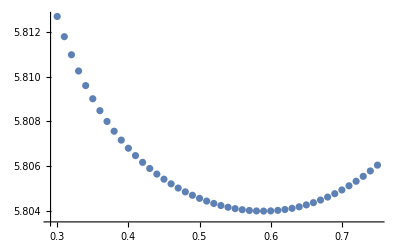

{9.86135,9.78881,9.7598,9.73409,9.71284,9.69876,9.67824,9.64488,9.64251,9.62776,9.61561,9.59181,9.58808,9.57912,9.53697,9.52833,9.49039,9.47309,9.46735,9.44776,9.27989,9.25352,9.25128,9.21979,9.20611,9.19285,9.17237,9.13806,9.12831,9.12078,8.42156,8.34063,8.31711,8.27732,8.25622,8.24506,8.22595,8.1738,8.16564,8.15244,8.12626,8.11746,8.10115,8.08862,8.049,8.03713,8.01373,8.00223,7.99859,7.98158,7.41642,7.33379,7.32306,7.28654,7.28303,7.25877,7.24784,7.1934,7.1824,7.14872,7.12735,6.99437,6.69422,6.61054,6.58188,6.56297,6.46563,6.33868,5.94383,5.80611}

Successfully Found Minimum

{0.59,5.80398}

```mathematica
(* Obtain a table of {{ω,E}} sets for varying ω to determine lowest Eigenvalue *)
tab=Table[{ω,Eigenvalues[Hb[J,P,Isospin,Λ,γMax,ω,m1,m2,m3,project]][[-firstNonZero]]-(2.02*10^-3)/(m1*m2*m3)},{ω,rangeMin,rangeMax,increment}];

(* Plot the list of above set of {{ω,E}} (The U-plot) *)
ListPlot[tab]

(* Extract ω's and Eigenvalues separately *)
omegas=tab[[All,1]];
evals=tab[[All,2]];
(* Find value of minimum eigenvalue *)
minEval=Min[evals];
(* Find positional index of minimum eigenvalue *)
posOfMinEval=Position[evals,minEval][[1,1]];
(* Use positional index of minimum eigenvalue to obtain the corresponding value of ω *)
optimumOmega=omegas[[posOfMinEval]];
(* Construct a list object containing {Subscript[ω, min],Subscript[E, min]} *)
minimum={optimumOmega,minEval};
(* Obtain wMin *)
wMin=minimum[[1]];

(* Print all eigenvalues for all ω's *)
Print[Eigenvalues[Hb[J,P,Isospin,Λ,γMax,optimumOmega,m1,m2,m3,project]]//Chop]

(* Initiate an error counter, will go up by one for each error encountered *)
errors=0;
(* First, check if the list object {Subscript[ω, min],Subscript[E, min]} exists in the list of all {{ω,E}} *)
If[tab[[posOfMinEval]]!=minimum,errors+=1;Print["Does not agree"]]
(* Check if Subscript[E, min] is the first element of {{ω,E}}, if True, extend ω range to the left *)
If[posOfMinEval==1,errors+=1;Print["Need to extend range more to the left"]]
(* Check if Subscript[E, min] is the last element of {{ω,E}}, if True, extend ω range to the right *)
If[posOfMinEval==Length[tab],errors+=1;Print["Need to extend range more to the right"]]
(* Finally if no errors encountered print {Subscript[ω, min],Subscript[E, min]} *)
If[errors==0,Print["Successfully Found Minimum"];Print[minimum];]

(* Save data *)
If[save==True,
fullPath=FileNameJoin[{dirPath,filename}];
Print["Successfully saved to:"];
Export[fullPath,tab]]
```

{0.4,0.5,0.6,0.7,0.8}

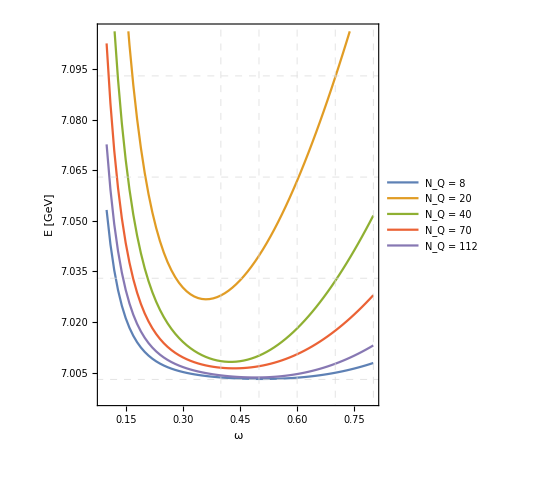

```mathematica
(* PLOTTING MASS PLOTS *)
allLinePaths=FileNames[All,"lines/Silvestre/eigenValues/scb"];
allFilenames=Table[FileNameJoin[{NotebookDirectory[],allLinePaths[[i]]}],{i,1,Length[allLinePaths]}];
allLinesData=Table[Import[allFilenames[[i]]],{i,1,Length[allFilenames]}];

plotRange={{0.09,0.8},Automatic};
frameTicks={{Automatic,None}, {Automatic,None}};
legendFontSize=14;
labelFontSize=14;
fontFamily="Times";
plotLegends={Placed[{Style["N_Q = 8",FontSize->legendFontSize,FontFamily->fontFamily],
Style["N_Q = 20",FontSize->legendFontSize,FontFamily->fontFamily],Style["N_Q = 40",FontSize->legendFontSize,FontFamily->fontFamily],
Style["N_Q = 70",FontSize->legendFontSize,FontFamily->fontFamily],
Style["N_Q = 112",FontSize->legendFontSize,FontFamily->fontFamily]
},{Center,Top}]};
labelStyle={FontSize->labelFontSize, FontFamily->fontFamily,Black};
frameLabel={{"E [GeV]",None},{"ω","Ω_cb, (scb)"}};
frame={{True,True},{True,True}};
vertGridLines=Table[7.003+x,{x,0,0.1,0.03}];
horzGridLines=Table[x,{x,0.4,0.8,0.1}]
gridLines={horzGridLines,vertGridLines};
gridLinesStyle=Directive[Dashed, LightGray];

plot=ListPlot[allLinesData,Joined->True,PlotRange->plotRange,
FrameTicks->frameTicks,
PlotLegends->plotLegends,
LabelStyle->labelStyle,
FrameLabel->frameLabel,
Frame->frame,
AspectRatio->1.2,
GridLines->gridLines,
GridLinesStyle->gridLinesStyle]
```

```mathematica
(* TODO: bb states plot up to 112, try 168 (γ=12),
TODO: understand what Silvestre means by quanta *)
```

```mathematica
Export["plots/baryons/eigVals/scbEvsW.pdf",plot,"PDF","AllowRasterization"->False]
```

plots/baryons/eigVals/scbEvsW.pdf

Expectation Values at ω_min: {55.0178,26.1531,35.4654}

Expectation Values as ratios: {0.475356,0.644617,1.}

ω_min: 0.63

```mathematica
silv={53.5,35.5,27.1};
Sort[silv/Max[silv]]
```

{0.506542,0.663551,1.}

{0.,-2.33928,0.,0.560751,0.106239,0.,0.,0.303791,0.,-0.240946,0.0016466,0.,0.,-0.111195,0.,-0.19898,0.00280398,0.,0.,-0.106032,0.,0.0768851,0.00677868,0.,0.,-0.00692993,0.0119665,0.,0.,0.0425701,0.0130784,0.,0.,-0.00109014,0.,0.0329691,0.00607814,0.,0.,0.0228662,0.,-0.0301249,0.000334949,0.,0.,-0.0129351,0.00353858,0.,0.,-0.015414,0.,-0.0274225,0.00351259,0.,0.,-0.0223389,0.00178249,0.,0.,-0.0273068,0.00185058,0.,0.,-0.0071179,0.,-0.0156817,0.00186192,0.,0.,-0.00772181}

{0,-0.953024,0,0.228451,0.0432818,0,0,0.123765,0,-0.0981616,0.000670825,0,0,-0.045301,0,-0.0810646,0.00114234,0,0,-0.0431978,0,0.0313231,0.00276164,0,0,-0.00282326,0.00487515,0,0,0.0173431,0.00532814,0,0,-0.000444125,0,0.0134316,0.00247624,0,0,0.00931573,0,-0.0122729,0.000136458,0,0,-0.00526979,0.00144162,0,0,-0.00627967,0,-0.0111719,0.00143103,0,0,-0.00910088,0.000726189,0,0,-0.0111248,0.000753927,0,0,-0.00289984,0,-0.00638872,0.000758548,0,0,-0.00314587}

2.45458

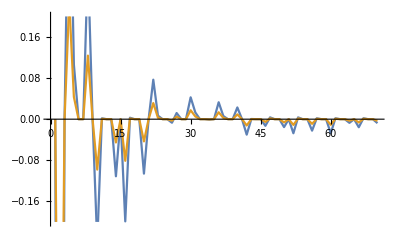

```mathematica
pos=36;
h=Hb[J,P,Isospin,Λ,γMax,minimum[[1]],m1,m2,m3,project]-IdentityMatrix[Length[sM]]*(2.02*10^-3)/(m1*m2*m3);
vec[pos_]:=Eigenvectors[h][[-pos]]//Chop
Hpsi=h.vec[pos]
Epsi=vec[pos]
Hpsi[[2]]/Epsi[[2]]
ListPlot[{Hpsi,Epsi},Joined->True,PlotRange->{-0.2,0.2}]
```